0.119114

0.001002

998

0.07273

0.0263

{{{{0.2104 (0.041331 v+1.89971 √(v^2))}}}}

8

{3.60888 v^2}

{261.95 v}

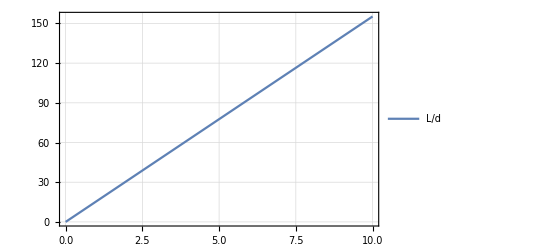

{{{{47.0937}}}}

{{{{{16.9874 v}}}}}

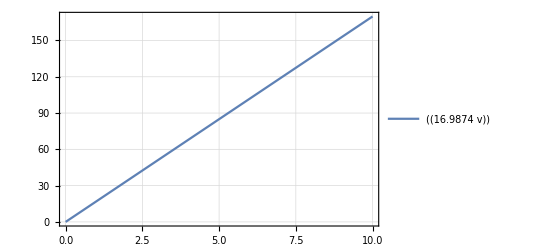

```mathematica
delta0=(3.1415*(2*(1+(3*eta0/((2*d*rho*sigma)^(1/2)))^(1/2)))^(1/2))*(2*d/2)
eta0=0.001002
rho=998
sigma=0.07273
d=0.0263
L=d*c*{{we}^{1/2}+{3*{we/re}}}
c=8
we=2*rho*{d/200}*v*v/sigma
re=2*rho*{d/200}*v/eta0
Plot[L/d,{v,0,10},PlotTheme->"Detailed"]

α={{sigma/{2*rho*{d/200}^{3}}}/{2+{{3*eta0}/{rho}}+{{rho/(sigma*d/100)}^{1/2}}}}^{1/2}
experimental=100*c*v/{α}
Plot[experimental,{v,0,10},PlotTheme->"Detailed"]
```

8

{3.60888 v^2}

{261.95 v}

-Graphics-

{{{{47.0937}}}}

{{{{{0.00169874 v}}}}}

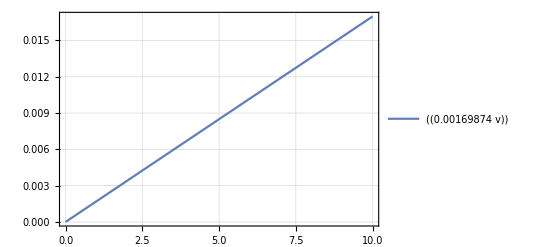

```mathematica
{{{0.0263 *10c (√we+(3 we)/re)}}}
```

```mathematica
2.2
```

2.2